```mathematica
(*Congettura di Collaz*)
```

```mathematica
a[0,n_]:=n;
a[i_,n_]:=
a[i,n]= If[EvenQ[ a[i-1,n]] , a[i-1,n]/2 , 3 a[i-1,n] +1   ];

collatz[k_]:=Do [  el= a[i,k];
                            Print[ " a [ ", i , " ] = "  , a[i] ];
   If [  el === 1,
  Print["Ci sono " ,i +1 ," Elementi"];
  Break[]
   ],
       {i,0,1000}
                                  ];
```

```mathematica
(* esempio con output della successione*)
collatz[76]
```

a [ 0 ] = 76

a [ 1 ] = 38

a [ 2 ] = 19

a [ 3 ] = 58

a [ 4 ] = 29

a [ 5 ] = 88

a [ 6 ] = 44

a [ 7 ] = 22

a [ 8 ] = 11

a [ 9 ] = 34

a [ 10 ] = 17

a [ 11 ] = 52

a [ 12 ] = 26

a [ 13 ] = 13

a [ 14 ] = 40

a [ 15 ] = 20

a [ 16 ] = 10

a [ 17 ] = 5

a [ 18 ] = 16

a [ 19 ] = 8

a [ 20 ] = 4

a [ 21 ] = 2

a [ 22 ] = 1

Ci sono 23 Elementi

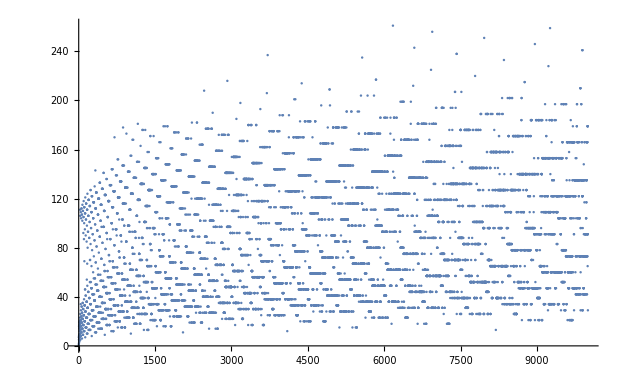

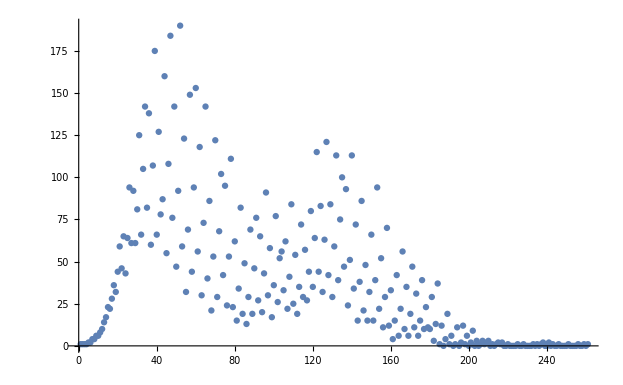

```mathematica
a[0,n_]:=n;
a[i_,n_]:=a[i,n]= If[EvenQ[ a[i-1,n]] , a[i-1,n]/2 , 3 a[i-1,n] +1   ];

collatz[k_]:=Do [  el= a[i,k];
                       
   If [  el === 1, Return[i];
  Break[]
   ],
       {i,0,10000}
                                  ];
   
punto[n_]:={n,collatz[n]}; 
ListPlot[ Table[  punto[x] , {x,1,10000}]]


list=Table[ collatz[t] , {t,1,10000}];
freq=Table[{i, Count[list,i]},{i,1,Max[list]}];
ListPlot[freq,PlotRange->All]
```